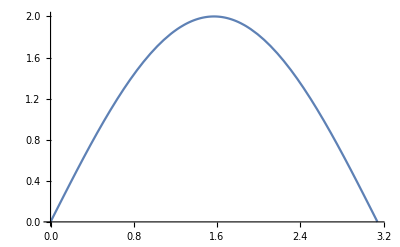

```mathematica
A[z_,β_,γ_]:=(β z^2 + γ(1+β)z + 1)/(z^2 + γ(1+β)z + β)
H[z_,β_,γ_]:=(1-A[z,β,γ])
z[ω_]:=ⅇ^(-ⅈ ω)
Plot[Abs[H[z[ω],0,0]],{ω,0,π},PlotRange->{0,2}]
```

#### The value of the integral is independent of γ

```mathematica
Plot3D[NIntegrate[Abs[H[z[ω],β,γ]],{ω,0,π}]/π,{β,0,0.99},{γ,-0.999,0.999}]
```

-Graphics3D-

So we can work out the value of the integral in 2D:

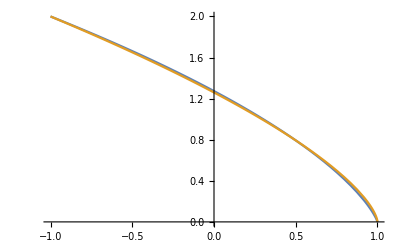

```mathematica
Plot[{NIntegrate[Abs[H[z[ω],β,0]],{ω,0,π}]/π,2((1-β)/2)^(1/1.5)},{β,-1,1}]
```

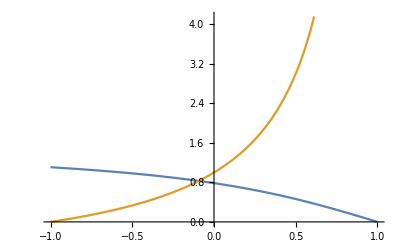

```mathematica
Plot[{ArcTan[1-β],(1+β)/(1-β),},{β,-1,1}]
```

```mathematica
gainToDb[g_]:=20 Log10[g]
dbToGain[db_]:=10^(db/20)

Heq[z_,fc_,bw_,gain_,fs_]:=Module[{α,β,D,b0,b1,b2,a1,a2},α=Tan[π bw/fs];
β=-Cos[2 π fc/fs];
D=If[gain<1,α+gain,α+1];
b0=If[gain<1,gain (1+α),(1+α gain)]/D;
b1=If[gain<1,2 β gain,2 β]/D;
b2=If[gain<1,gain (1-α),(1-α gain)]/D;
a1=If[gain<1,2 β gain,2 β]/D;
a2=If[gain<1,gain-α,1-α]/D;
(b0 z^2+b1 z+b2)/(z^2+a1 z+a2)]



fs=2 π;
Manipulate[LogPlot[Abs[Heq[z[ω],fc,fc/ⅇ^Q,dbToGain[g],fs] ],{ω,0,π},PlotRange->{dbToGain[-30],dbToGain[30]}],{{fc,1},0.01,π 0.999},{{Q,0},-3,3},{{g,5},-30,30}]
```

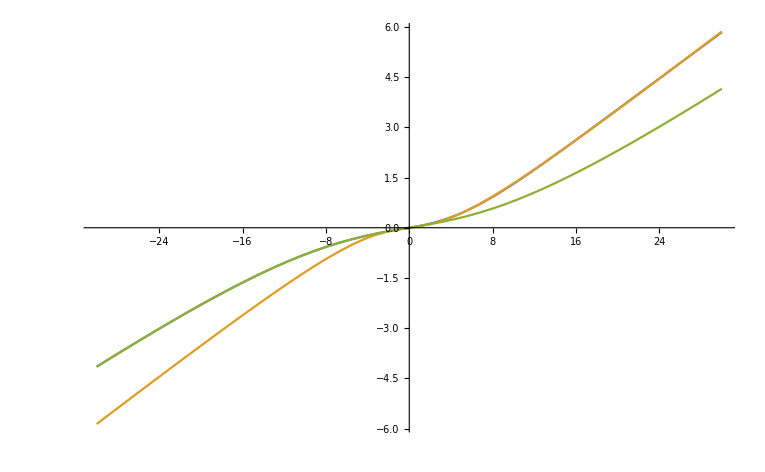

```mathematica
g1=6;
fc1=1;
Q1=2;
fs=2 π;
Plot[{Log[NIntegrate[Abs[Heq[z[ω],fc1,fc1/Q1,dbToGain[2 gain],fs]],{ω,0,π}]/(fs/2)], -0.9872196573908191ArcTan[gain(0.19932781862307056)]+gain(0.24159999847319052), -1.9613607114120637ArcTan[gain(0.08374879781693821)]+gain(0.21627948345499665)},{gain,-30,30}]
```

## Numerical Fit finding

```mathematica
positiveSide = Table[{x,Log[NIntegrate[Abs[Heq[z[ω],fc1,1/2,dbToGain[2 x],fs]],{ω,0,π}]/(fs/2)]},{x,0,30,0.1}];
negativeSide = Table[{x,Log[NIntegrate[Abs[Heq[z[ω],fc1,1/2,dbToGain[2 x],fs]],{ω,0,π}]/(fs/2)]},{x,-30,0,0.1}];
```

```mathematica
FindFit[positiveSide,γ ArcTan[α gain]+β gain,{α,β,γ},gain]
FindFit[negativeSide,γ ArcTan[α gain]+β gain,{α,β,γ},gain]
```

{α→0.199328,β→0.2416,γ→-0.98722}

{α→0.0837488,β→0.216279,γ→-1.96136}

Data over a range of Q values

```mathematica
dataQRange =Table[{x,Log[NIntegrate[Abs[Heq[z[ω],fc1,fc1/ⅇ^Q,dbToGain[x],fs]],{ω,0,π}]/(fs/2)]},{Q,-1-(1/2),-1+(1/2),1/16},{x,0,30,0.1}];
```

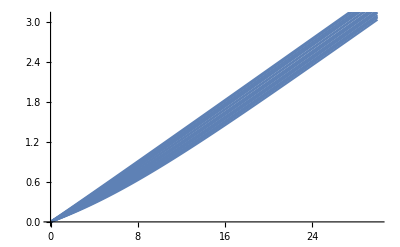

```mathematica
Show[ListLinePlot/@dataQRange]
```

It does not make sense to let the bandwidth of a bell filter exceed the Nyquist bandwidth. 
bandwidth = fc / Q. 
Therefore (fc/FNyquist) / Q < 1
finally, Q > fc / FNyquist

The plot below shows that the integral under the magnitude transfer function of a bell filter does indeed reach its peak near Q = fc / Nyquist, which in this case is 1/π:

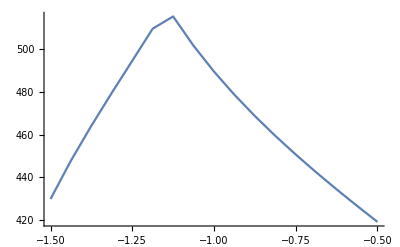

0.332871

0.31831

```mathematica
ListLinePlot[#[[2]]&/@Total/@dataQRange,DataRange->{-3/2,-1/2}]
ⅇ^-1.1
1/π //N
```

```mathematica
Table[
FindFit[
dataQRange[[i]],
γ ArcTan[gain/10]+0.125 gain,
{γ},gain],
{i,1,Length[dataQRange]}]
```

{{γ→-0.516302},{γ→-0.448462},{γ→-0.387248},{γ→-0.329798},{γ→-0.274102},{γ→-0.218583},{γ→-0.197539},{γ→-0.248147},{γ→-0.292845},{γ→-0.333223},{γ→-0.370365},{γ→-0.40504},{γ→-0.437808},{γ→-0.46909},{γ→-0.499206},{γ→-0.528407},{γ→-0.55689}}

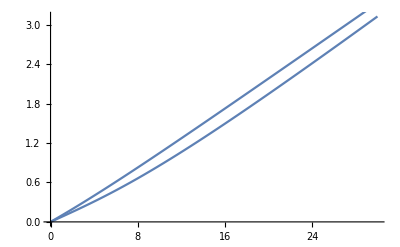

```mathematica
Show[Plot[-.5 ArcTan[gain/10]+0.125 gain,{gain,0,30}],ListLinePlot[dataQRange[[1]]]]
```

## Approximation of the integral under the EQ bell curve for